```mathematica
s = 2 Subscript[h, 0] x/a^2
```

(2 h_0 x)/a^2

```mathematica
1/Sqrt[1+s^2]//FullSimplify
```

1/(√((4 h_0^2 x^2)/a^4+1))

```mathematica
s/Sqrt[1+s^2]//FullSimplify
```

(2 h_0 x)/(a^2 √((4 h_0^2 x^2)/a^4+1))

```mathematica
h[x_]=x^2/4
```

x^2/4

```mathematica
x0=1.25
```

1.25

```mathematica
α[x_]=ArcTan[h'[x]]
```

tan^-1(x/2)

```mathematica
tauHat[x_]={Cos[α[x]],Sin[α[x]]}//FullSimplify
```

{2/(√(x^2+4)),x/(√(x^2+4))}

```mathematica
nHat[x_]={-Sin[α[x]],Cos[α[x]]}//FullSimplify
```

{-x/(√(x^2+4)),2/(√(x^2+4))}

```mathematica
jHat={0,1}
```

{0,1}

```mathematica
F = -Sqrt[2]jHat
```

{0,-√2}

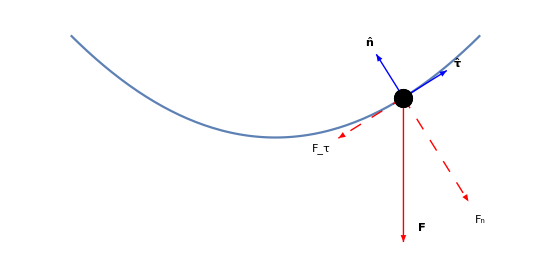

```mathematica
Plot[h[x],{x,-2,2},Frame->None,Axes->None,PlotRange->{{-2.2,2.2},{-1.1,1.1}},
AspectRatio->1/2,Epilog->{PointSize[0.025],Point[{x0,h[x0]}],Line[{{x0,h[x0]},{x0,h[x0]}}],
Thick,Blue,
Arrow[{{x0,h[x0]},{x0,h[x0]}+1/2tauHat[x0]}],
Arrow[{{x0,h[x0]},{x0,h[x0]}+1/2nHat[x0]}],
Black,Text[Style["τ̂",{Large,Bold}],{x0,h[x0]}+(1/2+1/8)tauHat[x0]],
Black,Text[Style["n̂",{Large,Bold}],{x0,h[x0]}+(1/2+1/8)nHat[x0]],
Black,Text[Style["F",{Large,Bold}],{x0,h[x0]}+Sqrt[2]{1/8,-0.9}],
Black,Text[Style["F",{Large,Italic,Bold}],{x0,h[x0]}+Sqrt[2]{1/8,-0.9}],
Black,Text[Style["F_n",{Large,Italic}],{x0,h[x0]}-Sqrt[2]nHat[x0]],
Black,Text[Style["F_τ",{Large,Italic}],{x0,h[x0]}-2Sqrt[2]/3tauHat[x0]],
Thick,Red,Arrow[{{x0,h[x0]},{x0,h[x0]}+F}],
Thick,Dashing[Medium], Red,
Arrow[{{x0,h[x0]},{x0,h[x0]}+(F.nHat[x0])nHat[x0]}],
Arrow[{{x0,h[x0]},{x0,h[x0]}+(F.tauHat[x0])tauHat[x0]}],
Black,
Point[{x0,h[x0]}]
}]
```

```mathematica
decomposeVec[A_,AB_,e1_,e2_]:=
```